```mathematica
Grid[MapThread[Prepend,{Prepend[Table[(2s k)^(s k),{s,2,5},{k,2,5}],{"s"->2,"s"->3,"s"->4,"s"->5}],{"","k"->2,"k"->3,"k"->4,"k"->5}}],Frame->All,Background->{None,{None,Yellow}}]
```

| s→2 | s→3 | s→4 | s→5
k→2 | 4096 | 2985984 | 4294967296 | 10240000000000
k→3 | 2985984 | 198359290368 | 36520347436056576 | 14348907000000000000000
k→4 | 4294967296 | 36520347436056576 | 1208925819614629174706176 | 109951162777600000000000000000000
k→5 | 10240000000000 | 14348907000000000000000 | 109951162777600000000000000000000 | 2980232238769531250000000000000000000000000

```mathematica
ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K]
```

```mathematica
activetriplets[nb_]:=({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4,Mod[(#-Mod[#,2])/2,2],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,8],4])
```

```mathematica
activetriplets[1]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,1}}

## Toutes les MT2 (inventaire presque complet) :

```mathematica
(*First Run*)       t=AbsoluteTime[];loop=halt=0;remise={};
remise=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<3,{activatedtriplet=activetriplets[nb][[4-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

0.3900007

0.4212007

0.3744007

```mathematica
remise
```

{102,118,196,198,204,212,214,220,228,230,236,244,246,252,454,462,470,478,486,494,502,510,614,630,708,710,716,724,726,732,740,742,748,756,758,764,1126,1142,1220,1222,1228,1236,1238,1244,1252,1254,1260,1268,1270,1276,1478,1486,1494,1502,1510,1518,1526,1534,1638,1654,1732,1734,1740,1748,1750,1756,1764,1766,1772,1780,1782,1788,2150,2166,2244,2246,2252,2260,2262,2268,2276,2278,2284,2292,2294,2300,2374,2382,2390,2398,2406,2414,2422,2430,2502,2510,2518,2526,2534,2542,2550,2558,2662,2678,2756,2758,2764,2772,2774,2780,2788,2790,2796,2804,2806,2812,3174,3190,3268,3270,3276,3284,3286,3292,3300,3302,3308,3316,3318,3324,3398,3406,3414,3422,3430,3438,3446,3454,3526,3534,3542,3550,3558,3566,3574,3582,3686,3702,3780,3782,3788,3796,3798,3804,3812,3814,3820,3828,3830,3836}

{Null,{{102,118,196,198,204,212,214,220,228,230,236,244,246,252,454,462,470,478,486,494,502,510,614,630,708,710,716,724,726,732,740,742,748,756,758,764,1126,1142,1220,1222,1228,1236,1238,1244,1252,1254,1260,1268,1270,1276,1478,1486,1494,1502,1510,1518,1526,1534,1638,1654,1732,1734,1740,1748,1750,1756,1764,1766,1772,1780,1782,1788,2150,2166,2244,2246,2252,2260,2262,2268,2276,2278,2284,2292,2294,2300,2374,2382,2390,2398,2406,2414,2422,2430,2502,2510,2518,2526,2534,2542,2550,2558,2662,2678,2756,2758,2764,2772,2774,2780,2788,2790,2796,2804,2806,2812,3174,3190,3268,3270,3276,3284,3286,3292,3300,3302,3308,3316,3318,3324,3398,3406,3414,3422,3430,3438,3446,3454,3526,3534,3542,3550,3558,3566,3574,3582,3686,3702,3780,3782,3788,3796,3798,3804,3812,3814,3820,3828,3830,3836}}}⟦1,2⟧

{{102,118,196,198,204,212,214,220,228,230,236,244,246,252,454,462,470,478,486,494,502,510,614,630,708,710,716,724,726,732,740,742,748,756,758,764,1126,1142,1220,1222,1228,1236,1238,1244,1252,1254,1260,1268,1270,1276,1478,1486,1494,1502,1510,1518,1526,1534,1638,1654,1732,1734,1740,1748,1750,1756,1764,1766,1772,1780,1782,1788,2150,2166,2244,2246,2252,2260,2262,2268,2276,2278,2284,2292,2294,2300,2374,2382,2390,2398,2406,2414,2422,2430,2502,2510,2518,2526,2534,2542,2550,2558,2662,2678,2756,2758,2764,2772,2774,2780,2788,2790,2796,2804,2806,2812,3174,3190,3268,3270,3276,3284,3286,3292,3300,3302,3308,3316,3318,3324,3398,3406,3414,3422,3430,3438,3446,3454,3526,3534,3542,3550,3558,3566,3574,3582,3686,3702,3780,3782,3788,3796,3798,3804,3812,3814,3820,3828,3830,3836}}

{Null,{{102,118,196,198,204,212,214,220,228,230,236,244,246,252,454,462,470,478,486,494,502,510,614,630,708,710,716,724,726,732,740,742,748,756,758,764,1126,1142,1220,1222,1228,1236,1238,1244,1252,1254,1260,1268,1270,1276,1478,1486,1494,1502,1510,1518,1526,1534,1638,1654,1732,1734,1740,1748,1750,1756,1764,1766,1772,1780,1782,1788,2150,2166,2244,2246,2252,2260,2262,2268,2276,2278,2284,2292,2294,2300,2374,2382,2390,2398,2406,2414,2422,2430,2502,2510,2518,2526,2534,2542,2550,2558,2662,2678,2756,2758,2764,2772,2774,2780,2788,2790,2796,2804,2806,2812,3174,3190,3268,3270,3276,3284,3286,3292,3300,3302,3308,3316,3318,3324,3398,3406,3414,3422,3430,3438,3446,3454,3526,3534,3542,3550,3558,3566,3574,3582,3686,3702,3780,3782,3788,3796,3798,3804,3812,3814,3820,3828,3830,3836}}}

0.3744007

0.3588006

0.3900007

0.3830219

0.3744006

0.3744006

0.3900007

```mathematica
{i,halt,loop,Length[Flatten[remise[[2]]]]}
```

{3,256,1632,160}

{3,256,1632,160}

{3,256,1632,160}

«2 more identical outputs»

```mathematica
remise1=Flatten[remise[[2]]];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[118].

```mathematica
Length[remise1]
```

160

160

160

«2 more identical outputs»

```mathematica
(*Second Run*)       t=AbsoluteTime[];
remise2=Reap[Do[         Clear[a]; i=0;nb=remise1[[j]];a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<8,{activatedtriplet=activetriplets[nb][[4-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{j,160}]];AbsoluteTime[]-t
```

Part::partd: Part specification remise1 ⟦ 1 ⟧ is longer than depth of object.

IntegerDigits::argb: IntegerDigits called with 4 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of IntegerDigits :: argb will be suppressed during this calculation.

Part::partw: Part 4 of {IntegerDigits[0, 0, 1/4\ (-Mod[remise1 ⟦ 1 ⟧, 2] - 2\ Mod[1/2\ Plus[« 2 »], 2] + remise1 ⟦ 1 ⟧), 2], IntegerDigits[0, 0, Mod[1/2\ (-Mod[Part[« 2 »], 2] + remise1 ⟦ 1 ⟧), 2], 0], IntegerDigits[0, 0, Mod[remise1 ⟦ 1 ⟧, 2], 0]} does not exist.

Part::partw: Part 3 of {IntegerDigits[0, 0, 1/4\ (-Mod[Part[« 2 »], 2] - 2\ Mod[Times[« 2 »], 2] + remise1 ⟦ 1 ⟧), 2], IntegerDigits[0, 0, Mod[1/2\ (-Mod[« 2 »] + remise1 ⟦ 1 ⟧), 2], 0], IntegerDigits[0, 0, Mod[remise1 ⟦ 1 ⟧, 2], 0]} ⟦ 4 ⟧ does not exist.

Table::iterb: Iterator {j, Min[-1, -2 + 2\ {IntegerDigits[« 4 »], IntegerDigits[« 4 »], IntegerDigits[« 4 »]} ⟦ 4 ⟧ ⟦ 3 ⟧], -2 + 2\ {IntegerDigits[0, 0, Times[« 2 »], 2], IntegerDigits[0, 0, Mod[« 2 »], 0], IntegerDigits[0, 0, Mod[« 2 »], 0]} ⟦ 4 ⟧ ⟦ 3 ⟧} does not have appropriate bounds.

Part::partd: Part specification remise1 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 4 of {IntegerDigits[0, 0, 1/4\ (-Mod[remise1 ⟦ 2 ⟧, 2] - 2\ Mod[1/2\ Plus[« 2 »], 2] + remise1 ⟦ 2 ⟧), 2], IntegerDigits[0, 0, Mod[1/2\ (-Mod[Part[« 2 »], 2] + remise1 ⟦ 2 ⟧), 2], 0], IntegerDigits[0, 0, Mod[remise1 ⟦ 2 ⟧, 2], 0]} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Table::iterb: Iterator {j, Min[-1, -2 + 2\ {IntegerDigits[« 4 »], IntegerDigits[« 4 »], IntegerDigits[« 4 »]} ⟦ 4 ⟧ ⟦ 3 ⟧], -2 + 2\ {IntegerDigits[0, 0, Times[« 2 »], 2], IntegerDigits[0, 0, Mod[« 2 »], 0], IntegerDigits[0, 0, Mod[« 2 »], 0]} ⟦ 4 ⟧ ⟦ 3 ⟧} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

0.2652

```mathematica
{i,halt,loop,Length[Flatten[remise2[[2]]]]}
```

{5,299,1747,2}

{5,299,1747,2}

{5,299,1747,2}

{8,299,1747,2}

{8,299,1747,2}

{8,299,1747,2}

```mathematica
remise2
```

{Null,{{3276,3292}}}

{Null,{{3276,3292}}}

{Null,{{3276,3292}}}

```mathematica
remise=Flatten[remise2[[2]]]
```

{3276,3292}

{3276,3292}

{3276,3292}

«1 more identical outputs»

## Progressive runs

```mathematica
(*First Run*)       t=AbsoluteTime[];loop=halt=0;remise={};
remise=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<3,{activatedtriplet=activetriplets[nb][[4-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

0.4056007

```mathematica
remise
```

{102,118,196,198,204,212,214,220,228,230,236,244,246,252,454,462,470,478,486,494,502,510,614,630,708,710,716,724,726,732,740,742,748,756,758,764,1126,1142,1220,1222,1228,1236,1238,1244,1252,1254,1260,1268,1270,1276,1478,1486,1494,1502,1510,1518,1526,1534,1638,1654,1732,1734,1740,1748,1750,1756,1764,1766,1772,1780,1782,1788,2150,2166,2244,2246,2252,2260,2262,2268,2276,2278,2284,2292,2294,2300,2374,2382,2390,2398,2406,2414,2422,2430,2502,2510,2518,2526,2534,2542,2550,2558,2662,2678,2756,2758,2764,2772,2774,2780,2788,2790,2796,2804,2806,2812,3174,3190,3268,3270,3276,3284,3286,3292,3300,3302,3308,3316,3318,3324,3398,3406,3414,3422,3430,3438,3446,3454,3526,3534,3542,3550,3558,3566,3574,3582,3686,3702,3780,3782,3788,3796,3798,3804,3812,3814,3820,3828,3830,3836}

```mathematica
t=AbsoluteTime[];loop=halt=0;remise={};
```

```mathematica
Do[
remise=Reap[Do[         Clear[a]; i=0;nb=remise[[j]];a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<jj,{activatedtriplet=activetriplets[nb][[4-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{j,Length[remise]}]][[2,1]],{jj,4,9}];AbsoluteTime[]-t
```

9.141616

```mathematica
{i,halt,loop,Length[remise]}
```

{9,299,1747,2}

```mathematica
remise
```

{3276,3292}

```mathematica
s=2;k=2;limit=60;Do[{Clear[tm];tm=TuringMachine[{ChangeNumbering[remise[[nb]],{2,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[remise[[nb]],{2,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[remise[[nb]]]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{nb,1,2}];Table[f[remise[[nb]]],{nb,1,2}]
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
(*Global Run*)       t=AbsoluteTime[];loop=halt=0;remise={};
remise=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<9,{activatedtriplet=activetriplets[nb][[4-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]];AbsoluteTime[]-t
```

0.9828017

0.8736015

0.7800014

0.7020013

0.6240011

1.952112

1.918803

1.934403

2164.264046

```mathematica
{halt,loop,Length[Flatten[remise[[2]]]]}
```

{299,1747,2}

{299,1746,3}

{299,1746,3}

{288,1744,16}

{288,1737,23}

{299,1747,2}

{299,1747,2}

{299,1747,2}

{332642,1159088,1262}

```mathematica
MyInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
```

```mathematica
activetriplets[nb_]:=MyInstructionsTable[nb,{2,2}][[All,2]]
```

```mathematica
FigureFromTriplet[{σ_,κ_,δ_},K_]:=σ 2 K+2 κ +δ
```

```mathematica
remise
```

{Null,{{3276,3292}}}

```mathematica
remise={3276,3292};
```

```mathematica
s=2;k=2;nb=remise[[1]];Clear[a,sigma,activetriplet,activatedtriplet];i=0;a[_]=0;n=ninf=-1;sigma=0;figures={};res={{1,0,-1,{0}}};While[n<0 && i<16 4096,{activatedtriplet=activetriplets[nb][[2s-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]]};figures=AppendTo[figures,FigureFromTriplet[activatedtriplet,2]];res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];(*Print[{nb,res}];*)
```

```mathematica
figures;
```

{4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,6,3,1,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,6,6,3,1,1,1,1,1,1,1,1,4,3}

```mathematica
figures3276={4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,6,3,1,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,6,6,3,1,1,1,1,1,1,1,1,4,3};
```

```mathematica
figures3276=figures;
```

```mathematica
u=Flatten[Position[figures3276,6]];
```

```mathematica
v=Length/@Split[u,#2-#1==1&];
```

```mathematica
w=Table[v[[4k]],{k,4 128}]
```

{3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,9,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,10,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,9,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,11,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,9,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,10,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,9,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,12}

```mathematica
ww=Table[w[[4k]],{k,4 32}]
```

{5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,9,5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,10,5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,9,5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,11,5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,9,5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,10,5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,9,5,6,5,7,5,6,5,8,5,6,5,7,5,6,5,12}

```mathematica
www=Table[ww[[4k]],{k,32}]
```

{7,8,7,9,7,8,7,10,7,8,7,9,7,8,7,11,7,8,7,9,7,8,7,10,7,8,7,9,7,8,7,12}

```mathematica
wwww=Table[www[[4k]],{k,8}]
```

{9,10,9,11,9,10,9,12}

```mathematica
∑_(n=0)^∞ q^(n^2+n)
```

EllipticTheta[2,0,q]/(2 q^(1/4))

```mathematica
∑_(n=0)^∞ q^(n^2)
```

1/2 (1+EllipticTheta[3,0,q])

```mathematica
Click for copyable input
```

```mathematica
Length[figures]
```

256

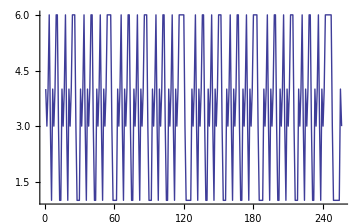

```mathematica
ListPlot[figures,Joined->True]
```

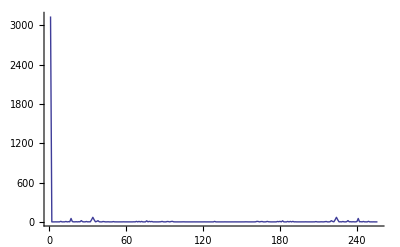

```mathematica
ListPlot[Abs[Fourier[figures]]^2,Joined->True]
```

```mathematica
Flatten[Table[{1,2,3,4},{j,64}]]
```

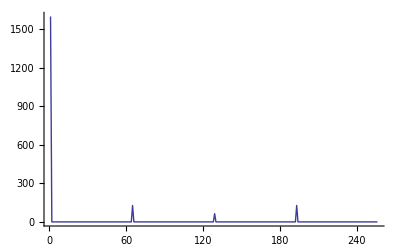

```mathematica
ListPlot[Abs[Fourier[Flatten[Table[{1,2,3,4},{j,64}]]]]^2,Joined->True]
```

```mathematica
Abs[Fourier[Flatten[Table[{1,2,3,4},{j,64}]]]]^2
```

{1600.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,128.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,64.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,128.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
s
```

3

```mathematica
remise[[28]]
```

87510

```mathematica
Solve[{a+b+c==1,4a+2b+c==3,9a+3b+c==6},{a,b,c}]
```

{{a→1/2,b→1/2,c→0}}

```mathematica
∑_(n=0)^∞ q^(n^2+n)
```

EllipticTheta[2,0,q]/(2 q^(1/4))

```mathematica
EllipticTheta[2,0,1/10]
```

EllipticTheta[2,0,1/10]

```mathematica
FindGeneratingFunction[{1,2,1,2,1,2,1},x]
```

(-1-2 x)/(-1+x^2)

```mathematica
FindGeneratingFunction[{1,2,1,2,2,1,2,2,2,1,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,2,1},x]
```

FindGeneratingFunction[{1,2,1,2,2,1,2,2,2,1,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,2,1},x]

```mathematica
FindSequenceFunction[{1,2,1,2,2,1,2,2,2,1,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,2,1},x]
```

FindSequenceFunction[{1,2,1,2,2,1,2,2,2,1,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,2,1},x]

```mathematica
Series[EllipticTheta[a,b,c q]/(2 q^(1/4)),{q,0,25}]
```

EllipticTheta[a,b,0]/(2 q^(1/4))+1/2 c EllipticTheta^(0,0,1)[a,b,0] q^(3/4)+1/4 c^2 EllipticTheta^(0,0,2)[a,b,0] q^(7/4)+1/12 c^3 EllipticTheta^(0,0,3)[a,b,0] q^(11/4)+1/48 c^4 EllipticTheta^(0,0,4)[a,b,0] q^(15/4)+1/240 c^5 EllipticTheta^(0,0,5)[a,b,0] q^(19/4)+(c^6 EllipticTheta^(0,0,6)[a,b,0] q^(23/4))/1440+(c^7 EllipticTheta^(0,0,7)[a,b,0] q^(27/4))/10080+(c^8 EllipticTheta^(0,0,8)[a,b,0] q^(31/4))/80640+(c^9 EllipticTheta^(0,0,9)[a,b,0] q^(35/4))/725760+(c^10 EllipticTheta^(0,0,10)[a,b,0] q^(39/4))/7257600+(c^11 EllipticTheta^(0,0,11)[a,b,0] q^(43/4))/79833600+(c^12 EllipticTheta^(0,0,12)[a,b,0] q^(47/4))/958003200+(c^13 EllipticTheta^(0,0,13)[a,b,0] q^(51/4))/12454041600+(c^14 EllipticTheta^(0,0,14)[a,b,0] q^(55/4))/174356582400+(c^15 EllipticTheta^(0,0,15)[a,b,0] q^(59/4))/2615348736000+(c^16 EllipticTheta^(0,0,16)[a,b,0] q^(63/4))/41845579776000+(c^17 EllipticTheta^(0,0,17)[a,b,0] q^(67/4))/711374856192000+(c^18 EllipticTheta^(0,0,18)[a,b,0] q^(71/4))/12804747411456000+(c^19 EllipticTheta^(0,0,19)[a,b,0] q^(75/4))/243290200817664000+(c^20 EllipticTheta^(0,0,20)[a,b,0] q^(79/4))/4865804016353280000+(c^21 EllipticTheta^(0,0,21)[a,b,0] q^(83/4))/102181884343418880000+(c^22 EllipticTheta^(0,0,22)[a,b,0] q^(87/4))/2248001455555215360000+(c^23 EllipticTheta^(0,0,23)[a,b,0] q^(91/4))/51704033477769953280000+(c^24 EllipticTheta^(0,0,24)[a,b,0] q^(95/4))/1240896803466478878720000+(c^25 EllipticTheta^(0,0,25)[a,b,0] q^(99/4))/31022420086661971968000000+O[q]^(101/4)

```mathematica
Table[-2-3 Floor[1/2 (-1+Sqrt[1+8 x])]+3 Floor[1/2 (-1+Sqrt[9+8 x])],{x,0,250}]
```

{1,-2,1,-2,-2,1,-2,-2,-2,1,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2}

```mathematica
e[0,n_]:=0;q[1,n_]=g[[n+1]]/g[[n]];
e[k_,n_]:=e[k,n]=e[k-1,n+1]+q[k,n+1]-q[k,n];
q[k_,n_]:=q[k,n]=e[k-1,n+1]q[k-1,n+1]/e[k-1,n];
```

Part::pspec: Part specification 1 + n is neither an integer nor a list of integers.

Part::pspec: Part specification n is neither an integer nor a list of integers.

```mathematica
Clear[g];g={2,1,2,2,1,2,2,2,1,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1};
```

```mathematica
g[[0]]=1
```

1

```mathematica
Table[q[m,0],{m,1,4}]
```

{2,-1/2,-5/3,0}

```mathematica
Table[e[m,0],{m,1,4}]
```

{-3/2,2/3,1,ComplexInfinity}

```mathematica
g[[1]]
```

2

```mathematica
1/(1-2z/(1+3/2z/(1+1/2z/(1-2/3z/(1+5/3z/(1-z))))))
```

```mathematica
Series[1/(1-2z/(1+3/2z/(1+1/2z/(1-2/3z/(1+5/3z/(1-z)))))),{z,0,20}]
```

1+2 z+z^2+2 z^3+2 z^4+z^5+2 z^6+2 z^7+z^8+2 z^9+2 z^10+z^11+2 z^12+2 z^13+z^14+2 z^15+2 z^16+z^17+2 z^18+2 z^19+z^20+O[z]^21

```mathematica
(* remise[[102]]=549976    !!Base 12!!  *)
```

```mathematica
{4,   3,4,    6,3,3,4,   6,6,3,3,3,4,    6,6,6,3,3,3,3,4,    6,6,6,6,3,3,3,3,3,4,        6,6,6,6,6,3,3,3,3,3,3,4,    6,6,6,6,6,6,3,3,3,3,3,3,3,4,    6,6}
```